```mathematica
refVol=Abs[Partition[BinaryReadList[NotebookDirectory[]<>"../test_data/8mm_iso_x_rot_0_5_to_2_5_deg_z_trans_rep_0_slice_"<>ToString[#]<>".dat","Complex64"],32]&/@Range[0,31,1]];
```

```mathematica
scale=1/Max[refVol]
```

15.3553

```mathematica
refVolScaled=scale * refVol;
```

```mathematica
BinaryWrite[NotebookDirectory[]<>"refVolInput.dat",refVolScaled,"Real64"];
```

```mathematica
newVolScaled=scale * Abs[Partition[BinaryReadList[NotebookDirectory[]<>"../test_data/8mm_iso_x_rot_0_5_to_2_5_deg_z_trans_rep_5_slice_"<>ToString[#]<>".dat","Complex64"],32]&/@Range[0,31,1]];
```

```mathematica
BinaryWrite[NotebookDirectory[]<>"newVolInput.dat",newVolScaled,"Real64"];
```

Compute the cooridinates of each point in the Fourier domain; note that Fourier coordinates are funny in that the origin is centered in the first voxel

```mathematica
fourierPoints=Function[{zDim,yDim,xDim},RotateLeft[Table[{i,j,k},{i,-zDim,zDim-1},{j,-yDim,yDim-1},{k,-xDim,xDim-1}],{zDim,yDim,xDim}]]@@(Dimensions[refVolScaled]/2);
```

```mathematica
Dimensions[fourierPoints]
```

{32,32,32,3}

Define the radial window function that will be applied in the Fourier domain

```mathematica
windowFunction[x_]:=If[x/16<0.75,1,CosineWindow[(x/16-0.75)/0.375]]
```

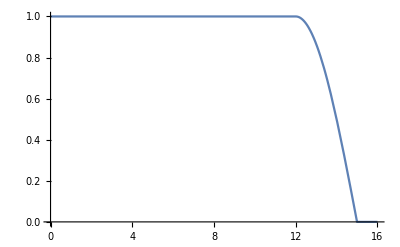

```mathematica
Plot[windowFunction[x],{x,0,16},PlotRange->All]
```

Compute the weight at each point in the Fourier domain

```mathematica
fourierWindowWeights=Map[windowFunction[Norm[#]]&,N[fourierPoints],{3}];
```

Define a function for applying the weights in the Fourier domain

```mathematica
filteredImage[img_]:=Chop[InverseFourier[Fourier[img,FourierParameters->{1, -1}] * fourierWindowWeights,FourierParameters->{1, -1}]];
```

Apply the Fourier-domain weights to each image volume

```mathematica
filteredRefVolScaled=filteredImage[refVolScaled];
```

```mathematica
filteredNewVolScaled=filteredImage[newVolScaled];
```

```mathematica
points=Function[{zDim,yDim,xDim},Table[{i-(zDim/2-0.5),j-(yDim/2-0.5),k-(xDim/2-0.5)},{i,0,zDim-1},{j,0,yDim-1},{k,0,xDim-1}]]@@{32,32,32};
```

```mathematica
pointWeights=(windowFunction[Norm[#]]&/@Flatten[points,2]);
```

```mathematica
z1=N[-2+Sqrt[3]]
```

-0.267949

```mathematica
c0=6;
```

```mathematica
computeG[x_,dataLength_]:=MapThread[Times,{FoldList[z1#1+#2&,x*c0],PadLeft[{1/(1-z1^dataLength)},dataLength,1]}]
```

```mathematica
computeYPlus[x_,dataLength_]:=Function[list,Append[MapIndexed[#1+z1^(#2[[1]])Last[list]&,list][[;;-2]],Last[list]]]@computeG[x,dataLength]
```

```mathematica
computeH[x_,dataLength_]:=Reverse[MapThread[Times,{FoldList[z1#1+#2&,Reverse[-z1 computeYPlus[x,dataLength]]]PadLeft[{1/(1-z1^dataLength)},dataLength,1]}]]
```

```mathematica
computeY[x_,dataLength_]:=Reverse[Function[list,Append[MapIndexed[#1+z1^(#2[[1]])Last[list]&,list][[;;-2]],Last[list]]]@Reverse[computeH[x,dataLength]]]
```

```mathematica
coeffImageBSpline[img_]:=Block[{
y},
(* Do x-direction calculation *)
y = Map[computeY[#,Dimensions[img][[3]]]&,img,{2}];
(* Do y-direction calculation *)
y = Map[computeY[#,Dimensions[y][[2]]]&,y];
(* Do z-direction calculation *)
y = computeY[y,Dimensions[y][[1]]];
Return[y];
];
```

This is the coefficient matrix that links the 64 coefficient values in the neighbourhood around a point, with the 64 powers of that point’s coordinates inside the cell..

```mathematica
bSplineCoeffMat={{1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0,1/54,2/27,1/54,0,2/27,8/27,2/27,0,1/54,2/27,1/54,0,0,0,0,0,1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0,-1/18,0,1/18,0,-2/9,0,2/9,0,-1/18,0,1/18,0,0,0,0,0,-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0,1/18,-1/9,1/18,0,2/9,-4/9,2/9,0,1/18,-1/9,1/18,0,0,0,0,0,1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0,-1/54,1/18,-1/18,1/54,-2/27,2/9,-2/9,2/27,-1/54,1/18,-1/18,1/54,0,0,0,0,-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0,-1/18,-2/9,-1/18,0,0,0,0,0,1/18,2/9,1/18,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0,1/6,0,-1/6,0,0,0,0,0,-1/6,0,1/6,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0,-1/6,1/3,-1/6,0,0,0,0,0,1/6,-1/3,1/6,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0,1/18,-1/6,1/6,-1/18,0,0,0,0,-1/18,1/6,-1/6,1/18,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0,1/18,2/9,1/18,0,-1/9,-4/9,-1/9,0,1/18,2/9,1/18,0,0,0,0,0,1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0,-1/6,0,1/6,0,1/3,0,-1/3,0,-1/6,0,1/6,0,0,0,0,0,-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0,1/6,-1/3,1/6,0,-1/3,2/3,-1/3,0,1/6,-1/3,1/6,0,0,0,0,0,1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0,-1/18,1/6,-1/6,1/18,1/9,-1/3,1/3,-1/9,-1/18,1/6,-1/6,1/18,0,0,0,0,-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0,-1/54,-2/27,-1/54,0,1/18,2/9,1/18,0,-1/18,-2/9,-1/18,0,1/54,2/27,1/54,0,-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0,1/18,0,-1/18,0,-1/6,0,1/6,0,1/6,0,-1/6,0,-1/18,0,1/18,0,1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0,-1/18,1/9,-1/18,0,1/6,-1/3,1/6,0,-1/6,1/3,-1/6,0,1/18,-1/9,1/18,0,-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216,1/54,-1/18,1/18,-1/54,-1/18,1/6,-1/6,1/18,1/18,-1/6,1/6,-1/18,-1/54,1/18,-1/18,1/54,1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,-1/18,-2/9,-1/18,0,-1/72,-1/18,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,1/6,0,-1/6,0,1/24,0,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,-1/6,1/3,-1/6,0,-1/24,1/12,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,1/18,-1/6,1/6,-1/18,1/72,-1/24,1/24,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,-1/6,-1/24,0,1/12,1/3,1/12,0,-1/24,-1/6,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,-1/8,0,-1/4,0,1/4,0,1/8,0,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,1/4,-1/8,0,1/4,-1/2,1/4,0,-1/8,1/4,-1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/8,1/8,-1/24,-1/12,1/4,-1/4,1/12,1/24,-1/8,1/8,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,-1/24,-1/6,-1/24,0,1/24,1/6,1/24,0,-1/72,-1/18,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,1/8,0,-1/8,0,-1/8,0,1/8,0,1/24,0,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,-1/8,1/4,-1/8,0,1/8,-1/4,1/8,0,-1/24,1/12,-1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,1/24,-1/8,1/8,-1/24,-1/24,1/8,-1/8,1/24,1/72,-1/24,1/24,-1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,-1/36,-1/9,-1/36,0,-1/9,-4/9,-1/9,0,-1/36,-1/9,-1/36,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,1/12,0,-1/12,0,1/3,0,-1/3,0,1/12,0,-1/12,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,-1/12,1/6,-1/12,0,-1/3,2/3,-1/3,0,-1/12,1/6,-1/12,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,1/36,-1/12,1/12,-1/36,1/9,-1/3,1/3,-1/9,1/36,-1/12,1/12,-1/36,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,1/12,1/3,1/12,0,0,0,0,0,-1/12,-1/3,-1/12,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/4,0,1/4,0,0,0,0,0,1/4,0,-1/4,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,1/4,-1/2,1/4,0,0,0,0,0,-1/4,1/2,-1/4,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,-1/12,1/4,-1/4,1/12,0,0,0,0,1/12,-1/4,1/4,-1/12,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,-1/12,-1/3,-1/12,0,1/6,2/3,1/6,0,-1/12,-1/3,-1/12,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,1/4,0,-1/4,0,-1/2,0,1/2,0,1/4,0,-1/4,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,-1/4,1/2,-1/4,0,1/2,-1,1/2,0,-1/4,1/2,-1/4,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,1/12,-1/4,1/4,-1/12,-1/6,1/2,-1/2,1/6,1/12,-1/4,1/4,-1/12,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,1/36,1/9,1/36,0,-1/12,-1/3,-1/12,0,1/12,1/3,1/12,0,-1/36,-1/9,-1/36,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,-1/12,0,1/12,0,1/4,0,-1/4,0,-1/4,0,1/4,0,1/12,0,-1/12,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,1/12,-1/6,1/12,0,-1/4,1/2,-1/4,0,1/4,-1/2,1/4,0,-1/12,1/6,-1/12,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,-1/36,1/12,-1/12,1/36,1/12,-1/4,1/4,-1/12,-1/12,1/4,-1/4,1/12,1/36,-1/12,1/12,-1/36,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1/216,-1/54,-1/216,0,-1/54,-2/27,-1/54,0,-1/216,-1/54,-1/216,0,0,0,0,0,1/72,1/18,1/72,0,1/18,2/9,1/18,0,1/72,1/18,1/72,0,0,0,0,0,-1/72,-1/18,-1/72,0,-1/18,-2/9,-1/18,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/216,1/54,1/216,0,1/54,2/27,1/54,0,1/216,1/54,1/216,0,0,0,0,0},{1/72,0,-1/72,0,1/18,0,-1/18,0,1/72,0,-1/72,0,0,0,0,0,-1/24,0,1/24,0,-1/6,0,1/6,0,-1/24,0,1/24,0,0,0,0,0,1/24,0,-1/24,0,1/6,0,-1/6,0,1/24,0,-1/24,0,0,0,0,0,-1/72,0,1/72,0,-1/18,0,1/18,0,-1/72,0,1/72,0,0,0,0,0},{-1/72,1/36,-1/72,0,-1/18,1/9,-1/18,0,-1/72,1/36,-1/72,0,0,0,0,0,1/24,-1/12,1/24,0,1/6,-1/3,1/6,0,1/24,-1/12,1/24,0,0,0,0,0,-1/24,1/12,-1/24,0,-1/6,1/3,-1/6,0,-1/24,1/12,-1/24,0,0,0,0,0,1/72,-1/36,1/72,0,1/18,-1/9,1/18,0,1/72,-1/36,1/72,0,0,0,0,0},{1/216,-1/72,1/72,-1/216,1/54,-1/18,1/18,-1/54,1/216,-1/72,1/72,-1/216,0,0,0,0,-1/72,1/24,-1/24,1/72,-1/18,1/6,-1/6,1/18,-1/72,1/24,-1/24,1/72,0,0,0,0,1/72,-1/24,1/24,-1/72,1/18,-1/6,1/6,-1/18,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/216,1/72,-1/72,1/216,-1/54,1/18,-1/18,1/54,-1/216,1/72,-1/72,1/216,0,0,0,0},{1/72,1/18,1/72,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,0,0,0,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/72,1/18,1/72,0,0,0,0,0},{-1/24,0,1/24,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,0,0,0,0,1/24,0,-1/24,0,0,0,0,0,-1/24,0,1/24,0,0,0,0,0},{1/24,-1/12,1/24,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,0,0,0,0,-1/24,1/12,-1/24,0,0,0,0,0,1/24,-1/12,1/24,0,0,0,0,0},{-1/72,1/24,-1/24,1/72,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,0,0,0,0,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/72,1/24,-1/24,1/72,0,0,0,0},{-1/72,-1/18,-1/72,0,1/36,1/9,1/36,0,-1/72,-1/18,-1/72,0,0,0,0,0,1/24,1/6,1/24,0,-1/12,-1/3,-1/12,0,1/24,1/6,1/24,0,0,0,0,0,-1/24,-1/6,-1/24,0,1/12,1/3,1/12,0,-1/24,-1/6,-1/24,0,0,0,0,0,1/72,1/18,1/72,0,-1/36,-1/9,-1/36,0,1/72,1/18,1/72,0,0,0,0,0},{1/24,0,-1/24,0,-1/12,0,1/12,0,1/24,0,-1/24,0,0,0,0,0,-1/8,0,1/8,0,1/4,0,-1/4,0,-1/8,0,1/8,0,0,0,0,0,1/8,0,-1/8,0,-1/4,0,1/4,0,1/8,0,-1/8,0,0,0,0,0,-1/24,0,1/24,0,1/12,0,-1/12,0,-1/24,0,1/24,0,0,0,0,0},{-1/24,1/12,-1/24,0,1/12,-1/6,1/12,0,-1/24,1/12,-1/24,0,0,0,0,0,1/8,-1/4,1/8,0,-1/4,1/2,-1/4,0,1/8,-1/4,1/8,0,0,0,0,0,-1/8,1/4,-1/8,0,1/4,-1/2,1/4,0,-1/8,1/4,-1/8,0,0,0,0,0,1/24,-1/12,1/24,0,-1/12,1/6,-1/12,0,1/24,-1/12,1/24,0,0,0,0,0},{1/72,-1/24,1/24,-1/72,-1/36,1/12,-1/12,1/36,1/72,-1/24,1/24,-1/72,0,0,0,0,-1/24,1/8,-1/8,1/24,1/12,-1/4,1/4,-1/12,-1/24,1/8,-1/8,1/24,0,0,0,0,1/24,-1/8,1/8,-1/24,-1/12,1/4,-1/4,1/12,1/24,-1/8,1/8,-1/24,0,0,0,0,-1/72,1/24,-1/24,1/72,1/36,-1/12,1/12,-1/36,-1/72,1/24,-1/24,1/72,0,0,0,0},{1/216,1/54,1/216,0,-1/72,-1/18,-1/72,0,1/72,1/18,1/72,0,-1/216,-1/54,-1/216,0,-1/72,-1/18,-1/72,0,1/24,1/6,1/24,0,-1/24,-1/6,-1/24,0,1/72,1/18,1/72,0,1/72,1/18,1/72,0,-1/24,-1/6,-1/24,0,1/24,1/6,1/24,0,-1/72,-1/18,-1/72,0,-1/216,-1/54,-1/216,0,1/72,1/18,1/72,0,-1/72,-1/18,-1/72,0,1/216,1/54,1/216,0},{-1/72,0,1/72,0,1/24,0,-1/24,0,-1/24,0,1/24,0,1/72,0,-1/72,0,1/24,0,-1/24,0,-1/8,0,1/8,0,1/8,0,-1/8,0,-1/24,0,1/24,0,-1/24,0,1/24,0,1/8,0,-1/8,0,-1/8,0,1/8,0,1/24,0,-1/24,0,1/72,0,-1/72,0,-1/24,0,1/24,0,1/24,0,-1/24,0,-1/72,0,1/72,0},{1/72,-1/36,1/72,0,-1/24,1/12,-1/24,0,1/24,-1/12,1/24,0,-1/72,1/36,-1/72,0,-1/24,1/12,-1/24,0,1/8,-1/4,1/8,0,-1/8,1/4,-1/8,0,1/24,-1/12,1/24,0,1/24,-1/12,1/24,0,-1/8,1/4,-1/8,0,1/8,-1/4,1/8,0,-1/24,1/12,-1/24,0,-1/72,1/36,-1/72,0,1/24,-1/12,1/24,0,-1/24,1/12,-1/24,0,1/72,-1/36,1/72,0},{-1/216,1/72,-1/72,1/216,1/72,-1/24,1/24,-1/72,-1/72,1/24,-1/24,1/72,1/216,-1/72,1/72,-1/216,1/72,-1/24,1/24,-1/72,-1/24,1/8,-1/8,1/24,1/24,-1/8,1/8,-1/24,-1/72,1/24,-1/24,1/72,-1/72,1/24,-1/24,1/72,1/24,-1/8,1/8,-1/24,-1/24,1/8,-1/8,1/24,1/72,-1/24,1/24,-1/72,1/216,-1/72,1/72,-1/216,-1/72,1/24,-1/24,1/72,1/72,-1/24,1/24,-1/72,-1/216,1/72,-1/72,1/216}};
```

Define a function that takes and image and all of its derivatives, and computes the interpolation coefficients

```mathematica
coeffs[img_]:=Transpose[bSplineCoeffMat. Function[coeffImg,RotateLeft[coeffImg,#]&/@Flatten[Table[{k,j,i},{k,-1,2},{j,-1,2},{i,-1,2}],2]]@(coeffImageBSpline[img]),{4,1,2,3}];
```

Define a function that takes a set of interpolation coefficients, a rotation matrix, a translation vector (and the dimensions of the image volume), and interpolates the image at a set of points

```mathematica
transformPoints[rotMatrix_,trans_,points_,dims_,halfDims_]:=
Block[{invRot=Inverse[rotMatrix]},
Return[Map[invRot . (#-trans)&,points,{3}]];
]
```

```mathematica
interpImg[coeffs_,interpGridPoints_,dims_,halfDims_]:=
Block[{
curInterpGridPoint=(Mod[# + halfDims - {0.5,0.5,0.5}+dims,dims]+{1,1,1})&/@Flatten[interpGridPoints,2],
coeffIndices,interVoxelPoints,interVoxelPointPowers},
coeffIndices=Floor[curInterpGridPoint];
interVoxelPoints=curInterpGridPoint-coeffIndices;
interVoxelPointPowers[interVoxelPoint_]:=Flatten[Outer@@Prepend[(Transpose[{{1,1,1},interVoxelPoint,interVoxelPoint^2,interVoxelPoint^3}]),Times]];
Return[
MapThread[
Function[{coeffIndex,interVoxelPoint},(coeffs[[#1,#2,#3]] &@@coeffIndex). interVoxelPointPowers[interVoxelPoint]],
{coeffIndices,interVoxelPoints}]];
]
```

```mathematica
interpImg[coeffs_,rotMatrix_,trans_,points_,dims_,halfDims_]:=
interpImg[coeffs,transformPoints[rotMatrix,trans,points,dims,halfDims],dims,halfDims];
```

```mathematica
Dimensions[coeffs[refVolScaled]]
```

{32,32,32,64}

Compute the cooridinates of each voxel in the image domain; note that image coordinates put the origin at the center of the image, so each voxel has a non-integer coordinate.

```mathematica
points=Function[{zDim,yDim,xDim},Table[{i-(zDim/2-0.5),j-(yDim/2-0.5),k-(xDim/2-0.5)},{i,0,zDim-1},{j,0,yDim-1},{k,0,xDim-1}]]@@{32,32,32};
```

```mathematica
Dimensions[points]
```

{32,32,32,3}

```mathematica
Dimensions[transformPoints[IdentityMatrix[3],{0,0,0},points,{32,32,32},{16,16,16}]]
```

{32,32,32,3}

```mathematica
Dimensions[interpImg[coeffs[refVolScaled],IdentityMatrix[3],{0,0,0},points,{32,32,32},{16,16,16}]]
```

{32768}

```mathematica
derivs[img_]:=Block[{
y,
derivX,
derivY,
derivZ},
(* Compute x-direction derivs *)
derivX=(RotateRight[img,{0,0,-1}]-RotateRight[img,{0,0,1}])/2;
(* Compute x-direction derivs *)
derivY=(RotateRight[img,{0,-1,0}]-RotateRight[img,{0,1,0}])/2;
derivZ=(RotateRight[img,{-1,0,0}]-RotateRight[img,{1,0,0}])/2;
Return[{derivX, derivY, derivZ}];
];
```

6D Registration

We want to find the linear approximation to the derivatives with respect to how an object rotating around a vector x by norm[x] radians, and then translating, will change the image. The M matrix represents this approximation, and is a function of the coordinate at which its being evaluated, so define a method to compute it given the coordinate. Note that because we’re describing the effect of moving the object, the signs are flipped vs in Martin’s paper. Also note that because my derivatives are stored in the order (dx, dy, dz), but my coordinates in the p-vector are (z,y,x,rz,ry,rx) I need to reverse the order of the rows vs in Martin’s paper.

```mathematica
M[x_]:= {{0,0,-1,-x[[2]],x[[1]],0},{0,-1,0,x[[3]],0,-x[[1]]},{-1,0,0,0,-x[[3]],x[[2]]}} ;
```

```mathematica
M[{z,y,x}]//MatrixForm
```

(0 | 0 | -1 | -y | z | 0
0 | -1 | 0 | x | 0 | -z
-1 | 0 | 0 | 0 | -x | y)

Compute the M matrix for every point in the image, giving an M tensor

```mathematica
MTensor[points_]:=Transpose[Map[M,points,{3}],{1,2,3,5,4}];
```

```mathematica
Dimensions[MTensor[points]]
```

{32,32,32,6,3}

Visualize the derivatives of the first image volume with respect to the six parameters

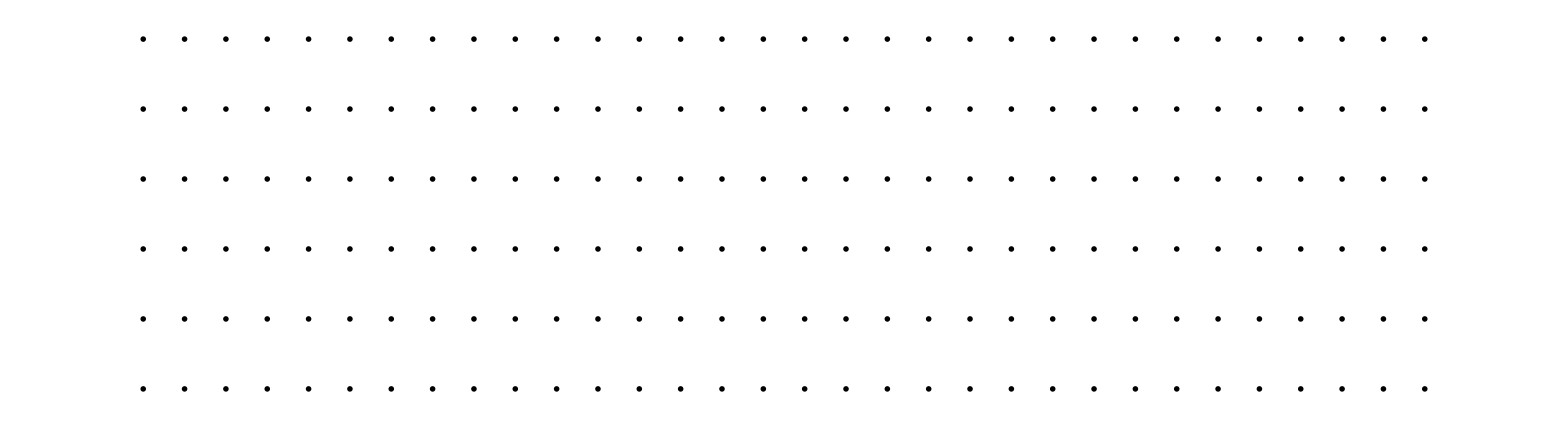

```mathematica
GraphicsGrid[Map[ArrayPlot[#,PixelConstrained->2]&,#/(2Max[#])+0.5,{2}]&@(Transpose[Partition[Partition[Flatten[MapThread[#1 . #2&,{MTensor[points],Transpose[derivs[filteredRefVolScaled],{4,1,2,3}]},3],2],32],32],{2,3,4,1}])]
```

```mathematica
Dimensions[(Transpose[Partition[Partition[Flatten[MapThread[#1 . #2&,{MTensor[points],Transpose[derivs[filteredRefVolScaled],{4,1,2,3}]},3],2],32],32],{2,3,4,1}])]
```

{6,32,32,32}

Given the gradient with respect to p, and the residual r, compute a Gauss Newton step

```mathematica
GaussNewtonStep[gradPTransGradP_,gradP_,r_]:=Block[
{deltaP,
JTransR=-Transpose[gradP] . r},
(*Print["JTransR" <> ToString[JTransR]];*)
deltaP=LinearSolve[gradPTransGradP,JTransR];
Return[deltaP]]
```

Define a utility function that takes a value of p, and prints the length of the translations in mm, the translation vector in mm, the angle of rotation in degrees, and the axis of rotation.

```mathematica
pToTransAndRot[p_]:={{Norm[p[[1;;3]]*8],p[[1;;3]]*8},{If[Norm[p[[4;;6]]]==0,0,Norm[p[[4;;6]]]/Degree],Normalize[p[[4;;6]]]}}
```

For clarity and debugging-value, let’s break these steps out and save the intermediate results in files, without all the trimming, etc.:

```mathematica
Norm[pointWeights *(Flatten[filteredRefVolScaled]-Flatten[filteredNewVolScaled])]
```

2.81664

```mathematica
Max[filteredRefVolScaled]
```

0.900536

```mathematica
Min[filteredRefVolScaled]
```

-0.0322055

```mathematica
Max[filteredNewVolScaled]
```

0.937795

```mathematica
Min[filteredNewVolScaled]
```

-0.0393063

```mathematica
Block[{
targetImg=filteredRefVolScaled,
movingImg=filteredNewVolScaled,
curPoints=points,
targetImgCoeffs,
residualGradP,
gradPTransGradP,
r,
prevNormR=$MaxMachineNumber,
deltaP,
p={0,0,0,0,0,0},
pList},
(* compute and save the interpolation coefficients for the target image *)
targetImgCoeffs=coeffs[targetImg];
(*Print["TargetImgCoeffs dimensions: " <>ToString[Dimensions[targetImgCoeffs]]];*)
(* compute and save the gradient of the moving image with respect to p *)
residualGradP=Transpose[(pointWeights * #)&/@Transpose[Flatten[MapThread[#1 . #2&,{MTensor[curPoints],Transpose[derivs[targetImg],{4,1,2,3}]},3],2]]];
Print["residualGradP[[1]]: " <>ToString[residualGradP[[1]]]];
gradPTransGradP=Transpose[residualGradP]. residualGradP;
(*Print["gradPTransGradP: " <>ToString[gradPTransGradP]];*)
(* now start the optimization *)
pList={p};
For[i=0,i<20,i++,
(* Compute and save the residual vector by: 1) interpolating the target image at all the points based on the current p, 2) subtracting this from the moving image, 3) multiplying this difference by the weights *)
(*Print[Dimensions[Flatten[points,2]]];*)
r=pointWeights *(interpImg[targetImgCoeffs,If[Norm[p[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[p[[4;;6]]],p[[4;;6]]]],p[[1;;3]],points,{32,32,32},{16,16,16}]-Flatten[movingImg]);
(*Print["r[[1]] " <> ToString[r[[1]]]];*)
(*Print["R_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[r]]];*)
(* take a Gauss Newton step, save the deltaP, and update p *)
Print[Norm[r]];
If[Norm[r]>prevNormR, 
pList=pList[[;;-2]];Break[],
prevNormR = Norm[r]];
deltaP = GaussNewtonStep[gradPTransGradP,residualGradP,r];
(*Print["DeltaP_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[deltaP]]];*)
p=p+deltaP;
(* append this new p to our list of previous states *)
pList=Append[pList,p];
Print[p];
Print[pToTransAndRot[p]]
];
BinaryWrite[NotebookDirectory[]<>"parameterOutput.dat",Last[pList],"Real64"]
]
```

residualGradP[[1]]: {0., 0., 0., 0., 0., 0.}

2.81664

{-0.00446733,-0.0459171,0.0142247,-0.0463988,0.000548899,-0.000426181}

{{0.386217,{-0.0357386,-0.367337,0.113797}},{2.65875,{-0.999888,0.0118287,-0.00918415}}}

1.6006

{-0.00373908,-0.0396451,0.0177525,-0.0375267,0.000549618,-0.0000671572}

{{0.348792,{-0.0299127,-0.317161,0.14202}},{2.15036,{-0.999891,0.0146444,-0.00178939}}}

1.52374

{-0.00357108,-0.0392602,0.0160745,-0.0381782,0.000452503,-0.000203388}

{{0.340588,{-0.0285687,-0.314082,0.128596}},{2.18764,{-0.999916,0.0118514,-0.00532687}}}

1.52254

{-0.00362627,-0.0393954,0.0163917,-0.0381058,0.00047172,-0.000176051}

{{0.342587,{-0.0290102,-0.315164,0.131134}},{2.18349,{-0.999913,0.0123781,-0.00461965}}}

1.52265

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_Ref_Grad_tests/parameterOutput.dat

```mathematica
Close[NotebookDirectory[]<>"parameterOutput.dat"]
```

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_Ref_Grad_tests/parameterOutput.dat

```mathematica
Block[{
targetImg=filteredRefVolScaled,
movingImg=filteredNewVolScaled,
dims={32,32,32},
halfDims={16,16,16},
sourceDerivs=Transpose[derivs[filteredRefVolScaled],{4,1,2,3}],
curPoints,
targetImgCoeffs,
residualGradP,
gradPTransGradP,
r,
prevNormR=$MaxMachineNumber,
deltaP,
p={0,0,0,0,0,0},
pList},
(* compute and save the interpolation coefficients for the target image *)
targetImgCoeffs=coeffs[targetImg];
(*Print["TargetImgCoeffs dimensions: " <>ToString[Dimensions[targetImgCoeffs]]];*)
(* compute and save the gradient of the moving image with respect to p *)
(* now start the optimization *)
pList={p};
For[i=0,i<20,i++,
(* Compute and save the residual vector by: 1) interpolating the target image at all the points based on the current p, 2) subtracting this from the moving image, 3) multiplying this difference by the weights *)
Print["Step: " <> ToString[i]];
Print["p: " <> ToString[p]];
curPoints=transformPoints[
If[Norm[p[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[p[[4;;6]]],p[[4;;6]]]],
p[[1;;3]],
points,
dims,halfDims];
r=pointWeights *(interpImg[targetImgCoeffs,curPoints,dims,halfDims]-Flatten[movingImg]);
(*Print["r[[1]] " <> ToString[r[[1]]]];*)
(*Print["R_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[r]]];*)
(* take a Gauss Newton step, save the deltaP, and update p *)
Print[Norm[r]];
If[Norm[r]>prevNormR, 
pList=pList[[;;-2]];Break[],
prevNormR = Norm[r]];
residualGradP=Transpose[(pointWeights * #)&/@Transpose[Flatten[MapThread[#1 . #2&,{MTensor[curPoints],Transpose[derivs[targetImg],{4,1,2,3}]},3],2]]];
gradPTransGradP=Transpose[residualGradP]. residualGradP;
(*Print[gradPTransGradP];*)
deltaP = GaussNewtonStep[gradPTransGradP,residualGradP,r];
(*Print["DeltaP_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[deltaP]]];*)
p=p+deltaP;
(* append this new p to our list of previous states *)
pList=Append[pList,p];
Print[p];
Print[pToTransAndRot[p]]
];
BinaryWrite[NotebookDirectory[]<>"gradientUpdateParameterOutput.dat",Last[pList],"Real64"]
]
```

Step: 0

p: {0, 0, 0, 0, 0, 0}

2.81664

{{44.8532,1.13754,0.958655,-7.94932,-76.5618,112.774},{1.13754,37.4047,-0.316572,87.7593,4.83362,44.7495},{0.958655,-0.316572,34.2703,-116.917,-41.7105,3.1157},{-7.94932,87.7593,-116.917,1877.52,161.607,95.0768},{-76.5618,4.83362,-41.7105,161.607,1486.2,-246.775},{112.774,44.7495,3.1157,95.0768,-246.775,1123.97}}

{-0.00446733,-0.0459171,0.0142247,-0.0463988,0.000548899,-0.000426181}

{{0.386217,{-0.0357386,-0.367337,0.113797}},{2.65875,{-0.999888,0.0118287,-0.00918415}}}

Step: 1

p: {-0.00446733, -0.0459171, 0.0142247, -0.0463988, 0.000548899, -0.000426181}

1.6006

{{44.8532,1.13754,0.958655,-7.34106,-80.7435,107.508},{1.13754,37.4047,-0.316572,87.6446,4.67565,45.0755},{0.958655,-0.316572,34.2703,-116.51,-42.0782,2.66541},{-7.34106,87.6446,-116.51,1879.48,156.617,102.294},{-80.7435,4.67565,-42.0782,156.617,1513.36,-223.717},{107.508,45.0755,2.66541,102.294,-223.717,1097.16}}

{-0.00374197,-0.0396079,0.0176855,-0.0375212,0.000559713,-0.0000903719}

{{0.348305,{-0.0299358,-0.316863,0.141484}},{2.15005,{-0.999886,0.0149155,-0.00240828}}}

Step: 2

p: {-0.00374197, -0.0396079, 0.0176855, -0.0375212, 0.000559713, -0.0000903719}

1.52376

{{44.8532,1.13754,0.958655,-7.45505,-80.2379,108.422},{1.13754,37.4047,-0.316572,87.9162,4.70692,45.0269},{0.958655,-0.316572,34.2703,-116.529,-41.9968,2.74813},{-7.45505,87.9162,-116.529,1879.17,157.515,101.303},{-80.2379,4.70692,-41.9968,157.515,1509.17,-228.765},{108.422,45.0269,2.74813,101.303,-228.765,1101.46}}

{-0.00360242,-0.0392593,0.0160731,-0.0381817,0.000446938,-0.000194968}

{{0.340598,{-0.0288194,-0.314074,0.128584}},{2.18783,{-0.999918,0.0117046,-0.0051059}}}

Step: 3

p: {-0.00360242, -0.0392593, 0.0160731, -0.0381817, 0.000446938, -0.000194968}

1.52253

{{44.8532,1.13754,0.958655,-7.4445,-80.2207,108.39},{1.13754,37.4047,-0.316572,87.8516,4.69807,45.0143},{0.958655,-0.316572,34.2703,-116.554,-42.0047,2.74642},{-7.4445,87.8516,-116.554,1879.16,157.485,101.224},{-80.2207,4.69807,-42.0047,157.485,1509.27,-228.34},{108.39,45.0143,2.74642,101.224,-228.34,1101.26}}

{-0.00364682,-0.039398,0.0163765,-0.038108,0.00046686,-0.000169913}

{{0.342573,{-0.0291745,-0.315184,0.131012}},{2.18361,{-0.999915,0.0122499,-0.00445834}}}

Step: 4

p: {-0.00364682, -0.039398, 0.0163765, -0.038108, 0.00046686, -0.000169913}

1.52265

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_Ref_Grad_tests/gradientUpdateParameterOutput.dat

```mathematica
Close[NotebookDirectory[]<>"gradientUpdateParameterOutput.dat"]
```

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_Ref_Grad_tests/gradientUpdateParameterOutput.dat

This axisAngle method is taken from http://mathematica.stackexchange.com/questions/29924/axis-angle-from-rotation-matrix

```mathematica
axisAngle[m_]:=Module[{axis,ovec,nvec},{axis,ovec}=Orthogonalize[{{1,-1,1} #,Permute[#,Cycles[{{1,3,2}}]]}]&@Extract[m-Transpose[m],{{3,2},{3,1},{2,1}}];
(*nvec is orthogonal to axis and ovec:*)nvec=Cross[axis,ovec];
{axis,Arg[Complex@@(((m.ovec).#&)/@{ovec,nvec})]}]
```

```mathematica
axisAngle[IdentityMatrix[3]]
```

{{0,0,0},0}

```mathematica
AccumulateParam[deltaParam_, oldParam_]:= Block[{
oldRotationMatrix=If[Norm[oldParam[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[oldParam[[4;;6]]],oldParam[[4;;6]]]],
deltaRotationMatrix=If[Norm[deltaParam[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[deltaParam[[4;;6]]],deltaParam[[4;;6]]]],
newRotationMatrix,
newRotationAxis,
newRotationAngle},
newRotationMatrix = oldRotationMatrix . deltaRotationMatrix;
{newRotationAxis, newRotationAngle}=axisAngle[newRotationMatrix];
Return[Join[oldRotationMatrix . deltaParam[[1;;3]]+oldParam[[1;;3]], newRotationAxis * newRotationAngle]];
]
```

```mathematica
Block[{
targetImg=filteredRefVolScaled,
movingImg=filteredNewVolScaled,
dims={32,32,32},
halfDims={16,16,16},
sourceDerivs=Transpose[derivs[filteredRefVolScaled],{4,1,2,3}],
curPoints,
targetImgCoeffs,
residualGradP,
gradPTransGradP,
r,
prevNormR=$MaxMachineNumber,
deltaP,
p={0,0,0,0,0,0},
pList},
(* compute and save the interpolation coefficients for the target image *)
targetImgCoeffs=coeffs[targetImg];
(*Print["TargetImgCoeffs dimensions: " <>ToString[Dimensions[targetImgCoeffs]]];*)
(* compute and save the gradient of the moving image with respect to p *)
(* now start the optimization *)
pList={p};
For[i=0,i<20,i++,
(* Compute and save the residual vector by: 1) interpolating the target image at all the points based on the current p, 2) subtracting this from the moving image, 3) multiplying this difference by the weights *)
Print["Step: " <> ToString[i]];
Print["p: " <> ToString[p]];
curPoints=transformPoints[
If[Norm[p[[4;;6]]]==0,IdentityMatrix[3],RotationMatrix[Norm[p[[4;;6]]],p[[4;;6]]]],
p[[1;;3]],
points,
dims,halfDims];
r=pointWeights *(interpImg[targetImgCoeffs,curPoints,dims,halfDims]-Flatten[movingImg]);
(*Print["r[[1]] " <> ToString[r[[1]]]];*)
(*Print["R_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[r]]];*)
(* take a Gauss Newton step, save the deltaP, and update p *)
Print[Norm[r]];
If[Norm[r]>prevNormR, 
pList=pList[[;;-2]];Break[],
prevNormR = Norm[r]];
residualGradP=Transpose[(pointWeights * #)&/@Transpose[Flatten[MapThread[#1 . #2&,{MTensor[curPoints],Transpose[derivs[targetImg],{4,1,2,3}]},3],2]]];
gradPTransGradP=Transpose[residualGradP]. residualGradP;
Print[gradPTransGradP];
deltaP = GaussNewtonStep[gradPTransGradP,residualGradP,r];
(*Print["DeltaP_"<>ToString[i]<>" dimensions: " <>ToString[Dimensions[deltaP]]];*)
p=AccumulateParam[deltaP,p];
(* append this new p to our list of previous states *)
pList=Append[pList,p];
Print[p];
Print[pToTransAndRot[p]]
];
BinaryWrite[NotebookDirectory[]<>"gradientUpdateComposeAccumulateParameterOutput.dat",Last[pList],"Real64"]
]
```

Step: 0

p: {0, 0, 0, 0, 0, 0}

2.81664

{{44.8532,1.13754,0.958655,-7.94932,-76.5618,112.774},{1.13754,37.4047,-0.316572,87.7593,4.83362,44.7495},{0.958655,-0.316572,34.2703,-116.917,-41.7105,3.1157},{-7.94932,87.7593,-116.917,1877.52,161.607,95.0768},{-76.5618,4.83362,-41.7105,161.607,1486.2,-246.775},{112.774,44.7495,3.1157,95.0768,-246.775,1123.97}}

{-0.00446733,-0.0459171,0.0142247,-0.0463988,0.000548899,-0.000426181}

{{0.386217,{-0.0357386,-0.367337,0.113797}},{2.65875,{-0.999888,0.0118287,-0.00918415}}}

Step: 1

p: {-0.00446733, -0.0459171, 0.0142247, -0.0463988, 0.000548899, -0.000426181}

1.6006

{{44.8532,1.13754,0.958655,-7.34106,-80.7435,107.508},{1.13754,37.4047,-0.316572,87.6446,4.67565,45.0755},{0.958655,-0.316572,34.2703,-116.51,-42.0782,2.66541},{-7.34106,87.6446,-116.51,1879.48,156.617,102.294},{-80.7435,4.67565,-42.0782,156.617,1513.36,-223.717},{107.508,45.0755,2.66541,102.294,-223.717,1097.16}}

{-0.00373743,-0.0394545,0.0173887,-0.0375211,0.000565587,-0.0000931134}

{{0.346225,{-0.0298994,-0.315636,0.13911}},{2.15005,{-0.999883,0.0150721,-0.00248134}}}

Step: 2

p: {-0.00373743, -0.0394545, 0.0173887, -0.0375211, 0.000565587, -0.0000931134}

1.52372

{{44.8532,1.13754,0.958655,-7.4557,-80.2247,108.429},{1.13754,37.4047,-0.316572,87.9052,4.70769,45.0274},{0.958655,-0.316572,34.2703,-116.534,-41.9964,2.74801},{-7.4557,87.9052,-116.534,1879.16,157.519,101.294},{-80.2247,4.70769,-41.9964,157.519,1509.12,-228.745},{108.429,45.0274,2.74801,101.294,-228.745,1101.49}}

{-0.00360469,-0.0393302,0.0161055,-0.0381816,0.000443875,-0.00019241}

{{0.341221,{-0.0288375,-0.314642,0.128844}},{2.18782,{-0.99992,0.0116244,-0.00503894}}}

Step: 3

p: {-0.00360469, -0.0393302, 0.0161055, -0.0381816, 0.000443875, -0.00019241}

1.52254

{{44.8532,1.13754,0.958655,-7.44432,-80.2222,108.386},{1.13754,37.4047,-0.316572,87.8528,4.69781,45.014},{0.958655,-0.316572,34.2703,-116.552,-42.0047,2.74651},{-7.44432,87.8528,-116.552,1879.15,157.481,101.222},{-80.2222,4.69781,-42.0047,157.481,1509.28,-228.338},{108.386,45.014,2.74651,101.222,-228.338,1101.25}}

{-0.00364659,-0.0393788,0.0163767,-0.038108,0.000467961,-0.000170539}

{{0.342432,{-0.0291727,-0.315031,0.131014}},{2.18362,{-0.999915,0.0122788,-0.00447476}}}

Step: 4

p: {-0.00364659, -0.0393788, 0.0163767, -0.038108, 0.000467961, -0.000170539}

1.52265

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_Ref_Grad_tests/gradientUpdateComposeAccumulateParameterOutput.dat

```mathematica
Close[NotebookDirectory[]<>"gradientUpdateComposeAccumulateParameterOutput.dat"]
```

/Users/dylan/Documents/Research/Students/Diana/MotionCorrection/Weighted_Gauss_Newton_Ref_Grad_tests/gradientUpdateComposeAccumulateParameterOutput.dat